# Real Scalar Field Theory

## Example Computations for a λϕ⁴ theory

## Define the Field

```mathematica
F = φ+ϕ;
sfields={ϕ};
UG ={ϕ->0};
VEV = {φ->u};
```

## Tree-Level Potential

### Scalar Potential

```mathematica
V=Expand[m^2/2*F^2+λ/4!*F^4];
V0=V/.UG
```

(m^2 φ^2)/2+(λ φ^4)/24

### Vacuum Expectation Values

```mathematica
Solve[D[V0,φ]==0/.{m->Sqrt[m2]},m2]/.VEV/.{m2->m^2}
```

{{m^2→-(u^2 λ)/6}}

```mathematica
Tadpole={m^2->-(u^2 λ)/6};
```

### Field Dependent Mass

```mathematica
MassMatrixScalars=Table[
D[D[V,sfields[[i]]],sfields[[j]]],{i,Length[sfields]},{j,Length[sfields]}
];
MassScalars=MassMatrixScalars/.UG//Simplify
PhysicalMassScalars = MassScalars/.VEV/.Tadpole//Simplify
```

{{m^2+(λ φ^2)/2}}

{{(u^2 λ)/3}}

## Coleman Weinberg

```mathematica
mϕ2[u_]:=m^2+(λ φ^2)/2
VCWi[m2_,Q_,d_,C_]:=d/(64*π^2)*m2^2*(Log[m2/Q^2]-C)
VCW[u_,Q_]:=VCWi[mϕ2[u],Q,1,3/2]
```

```mathematica
VCW[φ,μ]
```

((m^2+(λ φ^2)/2)^2 (-3/2+Log[(m^2+(λ φ^2)/2)/μ^2]))/(64 π^2)

## Renormalization Conditions

```mathematica
VEV={φ->u};
CT[x_]:=a/2*x^2+b/4!*x^4+c
```

```mathematica
(*Location of the VEV*)
D[CT[φ],φ]/.VEV
```

a u+(b u^3)/6

```mathematica
(*Mass of the field*)
D[CT[φ],{φ,2}]/.VEV
```

a+(b u^2)/2

```mathematica
(*Value of the potential*)
CT[φ]/.VEV
```

c+(a u^2)/2+(b u^4)/24

```mathematica
Solve[
Vux+a u+(b u^3)/6==0&&
Vuxx+a+(b u^2)/2==0&&
Vu+c+(a u^2)/2+(b u^4)/24==0,
{a,b,c}
]
```

{{a→-(3 Vux-u Vuxx)/(2 u),b→-(3 (-Vux+u Vuxx))/u^3,c→1/8 (-8 Vu+5 u Vux-u^2 Vuxx)}}

## Radiative Symmetry breaking

```mathematica
VRSB[x_]:=(λ x^4)/24+((m^2+(λ x^2)/2)^2 (-3/2+Log[(m^2+(λ x^2)/2)/μ^2]))/(64 π^2)/.m->0
VRSB[φ]
```

(λ φ^4)/24+(λ^2 φ^4 (-3/2+Log[(λ φ^2)/(2 μ^2)]))/(256 π^2)

```mathematica
D[VRSB[φ],φ]
```

(λ φ^3)/6+(λ^2 φ^3)/(128 π^2)+(λ^2 φ^3 (-3/2+Log[(λ φ^2)/(2 μ^2)]))/(64 π^2)

```mathematica
Solve[D[VRSB[φ],φ]==0,φ]
```

{{φ→-(√2 ⅇ^(1/2 (1-(32 π^2)/(3 λ))) μ)/(√λ)},{φ→(√2 ⅇ^(1/2 (1-(32 π^2)/(3 λ))) μ)/(√λ)}}

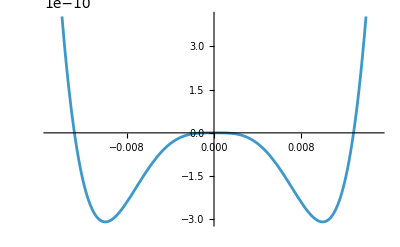

```mathematica
Plot[VRSB[φ]/.{λ->4*π, μ->1},{φ,-0.015,0.015}]
```